1

Plot of the 4 B-spline basis functions

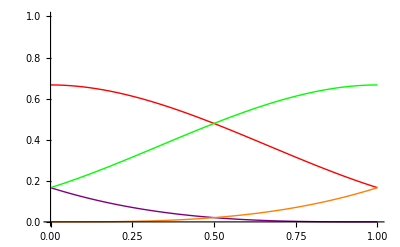

Plot of the σ functions (in orange), original function (in blue) and the points

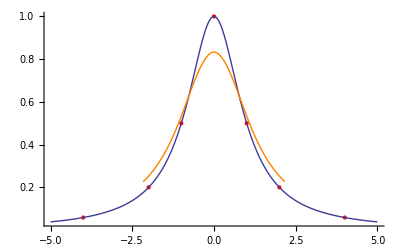

Comparing the polynomial interpolation of the points (in red) with the B-Spline σ functions (in orange). The interpolation does not exhibit local control.

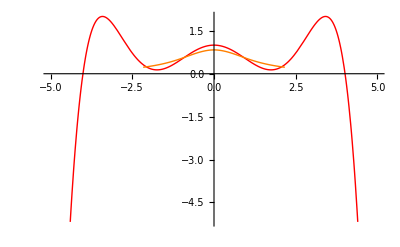

```mathematica
Clear[x,t,n,j,fplot,sigPlot,X1,Y]
f[x_]:=1/(1+x^2);
Subscript[P, 1]={-4,f[-4]};
Subscript[P, 2]={-2,f[-2]};
Subscript[P, 3]={-1,f[-1]};
Subscript[P, 4]={0,f[0]};
Subscript[P, 5]={1,f[1]};
Subscript[P, 6]={2,f[2]};
Subscript[P, 7]={4,f[4]};
j=1
n=7;
sigPlot={};
lPlot=ListPlot[{Subscript[P, 1],Subscript[P, 2],Subscript[P, 3],Subscript[P, 4],Subscript[P, 5],Subscript[P, 6],Subscript[P, 7]},PlotStyle->{Red}];
Subscript[p, 1][t_]:=1/6*(-t^3+3*t^2-3t+1);
Subscript[p, 2][t_]:=1/6*(3*t^3-6*t^2+4);
Subscript[p, 3][t_]:=1/6*(-3*t^3+3*t^2+3*t+1);
Subscript[p, 4][t_]:=1/6*(t^3);
While[j≤n-3,Subscript[σ, j][t_]:=Sum[Subscript[p, i][t]*Subscript[P, j+i-1],{i,1,4}];sigPlot=Append[{sigPlot},ParametricPlot[Subscript[σ, j][t],{t,0,1},PlotStyle->{Orange}]];
	j++;]
p1plot = Plot[Subscript[p, 1][t],{t,0,1},PlotRange->{{0,1},{0,1}}, PlotStyle->{Purple}];
p2plot = Plot[Subscript[p, 2][t],{t,0,1},PlotStyle->{Red}];
p3plot = Plot[Subscript[p, 3][t],{t,0,1},PlotStyle->{Green}];
p4plot = Plot[Subscript[p, 4][t],{t,0,1},PlotStyle->{Orange}];
fPlot =Plot[f[x], {x,-5,5}];
Print["Plot of the 4 B-spline basis functions"]
Show[p1plot,p2plot,p3plot,p4plot]
Print["Plot of the σ functions (in orange), original function (in blue) and the points"]
Show[lPlot,fPlot,sigPlot]
Print["Comparing the polynomial interpolation of the points (in red) with the B-Spline σ functions (in orange). The interpolation does not exhibit local control."]
Subscript[x, 1]=-4.;
Subscript[x, 2]=-2.;
Subscript[x, 3]=-1.;
Subscript[x, 4]=0;
Subscript[x, 5]=1.;
Subscript[x, 6]=2.;
Subscript[x, 7]=4.;
X1={{Subscript[x, 1]^0,Subscript[x, 1]^1,Subscript[x, 1]^2,Subscript[x, 1]^3,Subscript[x, 1]^4,Subscript[x, 1]^5,Subscript[x, 1]^6}, {Subscript[x, 2]^0,Subscript[x, 2]^1,Subscript[x, 2]^2,Subscript[x, 2]^3,Subscript[x, 2]^4,Subscript[x, 2]^5,Subscript[x, 2]^6},{Subscript[x, 3]^0,Subscript[x, 3]^1,Subscript[x, 3]^2,Subscript[x, 3]^3,Subscript[x, 3]^4,Subscript[x, 3]^5,Subscript[x, 3]^6},{1,Subscript[x, 4]^1,Subscript[x, 4]^2,Subscript[x, 4]^3,Subscript[x, 4]^4,Subscript[x, 4]^5,Subscript[x, 4]^6},{Subscript[x, 5]^0,Subscript[x, 5]^1,Subscript[x, 5]^2,Subscript[x, 5]^3,Subscript[x, 5]^4,Subscript[x, 5]^5,Subscript[x, 5]^6},
{Subscript[x, 6]^0,Subscript[x, 6]^1,Subscript[x, 6]^2,Subscript[x, 6]^3,Subscript[x, 6]^4,Subscript[x, 6]^5,Subscript[x, 6]^6},{Subscript[x, 7]^0,Subscript[x, 7]^1,Subscript[x, 7]^2,Subscript[x, 7]^3,Subscript[x, 7]^4,Subscript[x, 7]^5,Subscript[x, 7]^6}};
Y={f[Subscript[x, 1]],f[Subscript[x, 2]],f[Subscript[x, 3]],f[Subscript[x, 4]],f[Subscript[x, 5]],f[Subscript[x, 6]],f[Subscript[x, 7]]};
p[x_]:=1-0.62352*x^2+.12941*x^4-0.00588*x^6;
pPlot=Plot[p[x],{x,-5,5},PlotStyle->{Red}];
Show[pPlot,sigPlot]
```